```mathematica
(* vectors a, b  and c0 = a⊗b - initial vector in Subscript[H, 4] *)
a={2, -5};
b={-3, 7};
c0={a[[1]]*b[[1]], a[[1]]*b[[2]],a[[2]]*b[[1]],a[[2]]*b[[2]]}
```

```mathematica
(* Interaction matrix Subscript[V, 4×4] *)
V={{0, 0, 0, 0}, {0, -1, 1, 0}, {0, 1, -1, 0}, {0, 0, 0, 0}};
V//MatrixForm
```

(0 | 0 | 0 | 0
0 | -1 | 1 | 0
0 | 1 | -1 | 0
0 | 0 | 0 | 0)

```mathematica
(* function describing the evolution of the system, c(t)=e^iVt c(0)   *)
evolution[x_]:=MatrixExp[I V x].c0
```

```mathematica
(* moments of time *)
t=Range[0, 5, 0.001];
```

```mathematica
(* form list containing vectors 'c' at each moment of time *)
c={};
Do [
AppendTo[c, evolution[i]]
, {i, t}];
```

```mathematica
(* function returning nearest separable vector components *)
findNearestSeparable[c11_,c12_,c21_,c22_]:=FindMinimum[Norm[{c11-a1 b1,c12-a1 b2, c21-a2 b1,  c22-a2 b2},2],{a1, a2, b1, b2}];
```

```mathematica
(* calculating vectors 'a' and 'b' for which a⊗b is the closest separable vector for 'c' *)
ab={};
Do [
AppendTo[ab, findNearestSeparable[i[[1]], i[[2]],i[[3]],i[[4]]]]
, {i, c}];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

```mathematica
(* calculating c̃ = a⊗b for every moment of time*)
cwave={};
Do [
AppendTo[cwave, 
{(a1/.i[[2]])*(b1/.i[[2]]),(a1/.i[[2]])*(b2/.i[[2]]),(a2/.i[[2]])*(b1/.i[[2]]),(a2/.i[[2]])*(b2/.i[[2]])}]
, {i, ab}];
```

```mathematica
(* calculating g = c - c̃ *)
Clear[g];
g={};
Do [
AppendTo[g, c[[i]]-cwave[[i]]]
, {i, 5001}];
```

```mathematica
(* calculating norm of the vector g for every moment of time *)
Clear[gNorm]
gNorm={};
Do [
AppendTo[gNorm, Norm[i,2]]
, {i, g}];
```

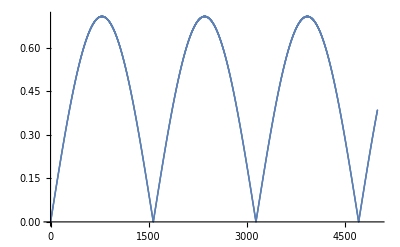

```mathematica
ListPlot[gNorm]
```